```mathematica
L1:=(-6 r^2 f[r]-3 r^3 f'[r]) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r])-2 r^3 f[r] NN''[r]
```

```mathematica
L2:=(-4 f[r]+4 f[r]^2-6 r f'[r]+10 r f[r] f'[r]) NN'[r]+NN[r] (-4 f'[r]+4 f[r] f'[r]+2 r f'[r]^2-2 r f''[r]+2 r f[r] f''[r])+(-4 r f[r]+4 r f[r]^2) NN''[r]
```

```mathematica
L3:=1/r^3(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))
```

```mathematica
L=Collect[Simplify[(L1/3+2*α*L2+3*(α^2)*L3)],{NN[r],NN'[r],NN''[r]}]
```

1/3 (-(54 α^2 (-1+f[r]) f[r]^2)/r^2-(81 α^2 (-1+f[r]) f'[r])/r-3 r^2 (2 f[r]+r f'[r])+(27 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/r^2+12 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r]))) NN'[r]+1/3 NN[r] (-r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+12 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+1/r^3 9 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))+1/3 (-2 r^3 f[r]+24 r α (-1+f[r]) f[r]-(54 α^2 (-1+f[r]) f[r])/r+(54 α^2 (-1+f[r]) f[r]^2)/r) NN''[r]

```mathematica
F0'[r_]:=Coefficient[L,NN[r]]
F1[r_]:=Coefficient[L,NN'[r]]
F2[r_]:=Coefficient[L,NN''[r]]
funcion3=Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

(r^4+3 α^2-(r^4+4 r^2 α+9 α^2) f[r]+α (2 r^2+9 α) f[r]^2-3 α^2 f[r]^3)/r^2

```mathematica
f3=f[r]/. Solve[funcion3==μ,f[r],Reals][[1]]
```

Root[-r^4-3 α^2+r^2 μ+(r^4+4 r^2 α+9 α^2) #1+(-2 r^2 α-9 α^2) #1^2+3 α^2 #1^3&,1]

```mathematica
q3=ToRadicals[f3]==0
```

-(-2 r^2 α-9 α^2)/(9 α^2)-(5 2^(1/3) r^4)/(9 (-38 r^6 α^3-486 r^2 α^5-243 r^2 α^4 μ+√(500 r^12 α^6+(-38 r^6 α^3-486 r^2 α^5-243 r^2 α^4 μ)^2))^(1/3))+((-38 r^6 α^3-486 r^2 α^5-243 r^2 α^4 μ+√(500 r^12 α^6+(-38 r^6 α^3-486 r^2 α^5-243 r^2 α^4 μ)^2))^(1/3))/(9 2^(1/3) α^2)==0

```mathematica
Clear[α,μ]
```

```mathematica
α:=0.03
μ:=1
```

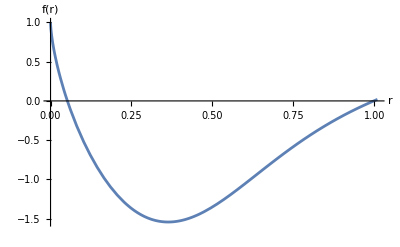

```mathematica
Plot[f3,{r,0,1.01},AxesLabel->{"r","f(r)"},PlotRange->All]
```

```mathematica
Solve[q3,r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(√(μ-√(-12 α^2+μ^2)))/(√2)},{r→(√(μ-√(-12 α^2+μ^2)))/(√2)},{r→-(√(μ+√(-12 α^2+μ^2)))/(√2)},{r→(√(μ+√(-12 α^2+μ^2)))/(√2)}}

```mathematica
(√(μ-√(-12 α^2+μ^2)))/(√2)
```

0.052032

```mathematica
(√(μ+√(-12 α^2+μ^2)))/(√2)
```

0.998645